# Thesis Notebook

## 2D Orbit now with dissipative forces

### Matex

```mathematica
(*1. GLOBAL CONFIGURATION*)Needs["MaTeX`"];
exportDirectory="/home/em/Documents/thesis/constant_density";
If[!FileExistsQ[exportDirectory],CreateDirectory[exportDirectory]];

(*Global Styling Variables*)
$ThesisFontSize=20;
$ThesisTickSize=14;
$ThesisImageSize=450; (*Slightly larger as requested*)
$ThesisThickness=2.0;
$GridStyle=Directive[GrayLevel[0.9],AbsoluteThickness[0.5]];
$FrameStyle=Directive[Black,AbsoluteThickness[1.2]];

(*REVERTED TO ORIGINAL COLORS*)
$ThesisColors={Blue,Red,Green,Purple,Darker[Green]};

SetOptions[MaTeX,"Preamble"->{"\\usepackage{amsmath, amsfonts, amssymb, amsthm, bm, lmodern}","\\newcommand{\\rb}{\\bar{r}}","\\providecommand{\\e}[1]{\\ensuremath{\\times 10^{#1}}}"}];

ThesisStandardPlot[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f(\\rb)",xLabel_:"\\rb",labels_List:{},xTick_:None,pPoints_:100,wPrec_:30]:=(*Defaulting to 30 digits of precision for 10^-23 scales*)Module[{finalPlot,plotOptions,fullPath,ticks,grid},ticks={Automatic,Automatic};
grid=Automatic;
If[xTick=!=None,ticks={{Automatic,Automatic},{Union[FindDivisions[{vMin,vMax},6],{{xTick,MaTeX["\\rb_0",FontSize->$ThesisFontSize]}}],Automatic}};
grid={{xTick},Automatic};];
plotOptions={Frame->True,Axes->False,PlotStyle->Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->Scaled[0.04],(*CRITICAL FOR HIGH ACCURACY*)PlotPoints->pPoints,MaxRecursion->6,(*High recursion to smooth out tiny variations*)WorkingPrecision->wPrec,(*Forces Mathematica to use arbitrary-precision math*)Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize-4,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Standard (High-Precision): ",Green,Bold],fullPath];
finalPlot]

(*2b.TIME PLOT FUNCTION-Updated for Round Numbers*)
ThesisStandardPlotTime[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f(\\bar{r})",xLabel_:"\\bar{r}",labels_List:{},xTick_:None]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,xDivs,proximityThreshold},ticks={Automatic,Automatic};grid={Automatic,Automatic};
If[xTick=!=None,xDivs=FindDivisions[{vMin,vMax},6];(*Forces nice round numbers*)proximityThreshold=(vMax-vMin)*0.08;
ticks={{Automatic,Automatic},{Union[Select[xDivs,Abs[#-xTick]>proximityThreshold&],{{xTick,MaTeX["t_{\\text{s}}",FontSize->$ThesisFontSize]}}],None}};];
plotOptions={Frame->True,Axes->False,PlotStyle->Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->{Scaled[0.02],Scaled[0.1]},Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize-4,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[funcs,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Time Plot: ",Green,Bold],fullPath];finalPlot]

(*2c.PIECEWISE PLOT FUNCTION-Updated for Round Numbers*)
ThesisPiecewisePlot[func_,{var_,vMin_,vMax_},rStar_,fileName_String,yLabel_:"f(\\bar{r})",xLabel_:"\\bar{r}",labels_List:{},xTick_:None]:=Module[{finalPlot,plotOptions,fullPath,ticks,grid,xDivs,proximityThreshold},ticks={Automatic,Automatic};grid={Automatic,Automatic};
If[xTick=!=None,xDivs=FindDivisions[{vMin,vMax},6];
proximityThreshold=(vMax-vMin)*0.08;
ticks={{Automatic,Automatic},{Union[Select[xDivs,Abs[#-xTick]>proximityThreshold&],{{xTick,MaTeX["\\rb_0",FontSize->$ThesisFontSize]}}],None}};];
plotOptions={Frame->True,Axes->False,ColorFunction->Function[{x,y},If[x<rStar,Blue,Red]],ColorFunctionScaling->False,PlotStyle->{AbsoluteThickness[$ThesisThickness+0.5]},FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->All,PlotRangePadding->{Scaled[0.02],Scaled[0.1]},Exclusions->None,Method->{"DefaultBoundaryStyle"->None}};
finalPlot=If[Length[labels]>0,Plot[func,{var,vMin,vMax},Evaluate[plotOptions],PlotLegends->Placed[LineLegend[{Blue,Red},MaTeX/@labels,LegendMarkerSize->30,LabelStyle->{FontSize->$ThesisFontSize-4,FontFamily->"Latin Modern Roman"}],{0.8,0.75}]],Plot[func,{var,vMin,vMax},Evaluate[plotOptions]]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Piecewise: ",Green,Bold],fullPath];finalPlot]

(*3. MASTER ORBIT FUNCTION*)
ThesisOrbitPlot[{xFunc_,yFunc_},{var_,vMin_,vMax_},rStar_,fileName_String,xLabel_:"\\bar{r}(t)\\cos(\\phi(t))",yLabel_:"\\bar{r}(t)\\sin(\\phi(t))",xTick_:None]:=Module[{orbitLine,body,finalPlot,fullPath,ticks,extras,startPos,plotBoundaries,xDivs,xRangeWidth},orbitLine=ParametricPlot[{xFunc,yFunc},{var,vMin,vMax},PlotStyle->{Darker[Blue],AbsoluteThickness[1.5]},PlotPoints->300];
body=Graphics[{Cyan,EdgeForm[{Cyan,AbsoluteThickness[1]}],Disk[{0,0},rStar]}];
ticks={Automatic,Automatic};extras={};
If[xTick=!=None,startPos={xFunc,yFunc}/. var->vMin;
extras={Directive[GrayLevel[0.4],Dashed,AbsoluteThickness[1]],InfiniteLine[{xTick,0},{0,1}],Directive[Black],Disk[startPos,Offset[3]]};
plotBoundaries=PlotRange/. AbsoluteOptions[orbitLine,PlotRange];
xRangeWidth=Abs[plotBoundaries[[1,2]]-plotBoundaries[[1,1]]];
xDivs=FindDivisions[plotBoundaries[[1]],6];
xDivs=Select[xDivs,Abs[#-xTick]>0.10*xRangeWidth&];
ticks={{Automatic,Automatic},{Union[Table[{i,i},{i,xDivs}],{{xTick,MaTeX["\\rb_0",FontSize->$ThesisFontSize]}}],Automatic}};];
finalPlot=Show[body,Graphics[extras],orbitLine,Frame->True,Axes->False,AspectRatio->Automatic,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->Automatic,GridLinesStyle->$GridStyle,ImageSize->$ThesisImageSize,PlotRange->All,PlotRangePadding->Scaled[0.08]];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Orbit: ",Blue,Bold],fullPath];finalPlot]

(*4. LOGARITHMIC PLOTTING FUNCTION*)
ThesisLogPlot[funcs_,{var_,vMin_,vMax_},fileName_String,yLabel_:"f",xLabel_:"t",tSurface_:None]:=Module[{finalPlot,fullPath,ticks,grid},grid={If[NumberQ[tSurface],{tSurface},{}],Automatic};
ticks={Automatic,{Join[FindDivisions[{vMin,vMax},6],If[NumberQ[tSurface],{{tSurface,MaTeX["t_{\\text{s}}",FontSize->$ThesisFontSize]}},{}]],Automatic}};
finalPlot=LogPlot[funcs,{var,vMin,vMax},Frame->True,Axes->False,PlotStyle->Table[{$ThesisColors[[Mod[i-1,Length[$ThesisColors]]+1]],AbsoluteThickness[$ThesisThickness]},{i,Length[Flatten[{funcs}]]}],FrameStyle->$FrameStyle,FrameTicks->ticks,FrameTicksStyle->Directive[Black,$ThesisTickSize],GridLines->grid,GridLinesStyle->$GridStyle,FrameLabel->{MaTeX[xLabel,FontSize->$ThesisFontSize],MaTeX[yLabel,FontSize->$ThesisFontSize]},ImageSize->$ThesisImageSize,AspectRatio->1/GoldenRatio,PlotRange->{{vMin,vMax},All},PlotRangePadding->{None,Scaled[0.05]},Method->{"DefaultBoundaryStyle"->None}];
fullPath=FileNameJoin[{exportDirectory,fileName<>".pdf"}];
Export[fullPath,finalPlot,"PDF"];
Print[Style["Saved Log Plot: ",Magenta,Bold],fullPath];finalPlot]
```

## Setting functions up and choosing variables

## Star constants

```mathematica
(*From wikipedia paper*)
```

```mathematica
infprec[lowlyprecision_, p_] := 10^-p Round[(10^p) lowlyprecision]
```

```mathematica
Msol = 1.989 10^30;
G = 6.6743 10^-11;
c = 3 10^8;
```

```mathematica
Mdummy = (G 1.4Msol)/c^2
```

2065.03

```mathematica
Rdummy = (12 10^3)/Mdummy;
R = infprec[Rdummy, 40];
Precision[R]
```

∞

```mathematica
(*R values in Schwarzschild coordinates*)
RStar = R;(*Radius of the Star*)
M = 1;
```

## Exterior Schwarzschild Isotropic coordinates definitions r(r̄), r̄(r), A(r̄), α(r̄)

### r(r̄), r̄(r) definitions

```mathematica
rofrbarOutside[rbar_] :=rbar (1 + M/(2 rbar))^2; 

rbarofrOutside[r_] := 1/2 (-M + r + Sqrt[r^2 - 2 M r]);
```

### Lapse and shift

```mathematica
A[rbar_] :=(1 + M/(2 rbar))^2;
α[rbar_] :=(1 - M/(2 rbar))/(1 + M/(2 rbar));
```

```mathematica
rbarStarrr = rbarofrOutside[RStar];
rbarStar = infprec[rbarStarrr, 40];
Precision[rbarStar]
```

∞

## TOV ρ=constant Isotropic coords definitions

### Mass function

```mathematica
Mfunc[r_] = Piecewise[{{M r^3/RStar^3, r < RStar}, {M, r>=RStar}}];
```

### r(r̄), r̄(r) for the interior

```mathematica
κ = √(2 M/RStar^3);
(*Integral constant I used by hand*)
Const = rbarofrOutside[RStar] √((1+√(1-(2M)/RStar))/(1-√(1-2 M/RStar)));(*This is the constant to match up the metrics*)
```

```mathematica
rbarofrInside[r_]:=Const √((1-√(1-2 Mfunc[r]/r))/(1+√(1-2 Mfunc[r]/r)));
rofrbarInside[rbar_]:=1/κ √(1-Tanh[Log[rbar/Const]]^2);
```

### Lapse and shift functions

```mathematica
αInside[rbar_]:=(3/2 √(1-2 M/RStar)-1/2 √(1-2(M rofrbarInside[rbar]^2)/RStar^3)); (*Lapse*)
AInside[rbar_]:=rofrbarInside[rbar]/rbar;(*Shift*)
```

## Setting up everything to solve the system of ODEs in 2D with dissipative forces

### Constants used

```mathematica
(*mass of PBH*)
rhodummy = 3/(4Pi RStar^3);
asos = 0.5; (*relativistic speed of sound*)
a = infprec[asos, 2];
ρ = infprec[rhodummy, 40];
Precision[ρ];
```

### Pressure function derived analytically

```mathematica
P[rbar_] = ρ((√(1 - 2(M r^2)/RStar^3)-√(1 - 2 M/RStar))/(3 √(1 - 2 M/RStar) - √(1 - 2(M r^2)/RStar^3))) /.r->rofrbarInside[rbar];
(*Derived from TOV as I done last year*)
```

### Mach number interpolation

#### Interpolating

```mathematica
fMachLow[m_] := 1/2 Log[(1+ m)/(1 - m)] - m ;
fMachhigh[m_] := 1/2 Log[1 - 1/m^2]  + 10
```

```mathematica
x1=9999/10000;
x2=10001/10000;
y1=fMachLow[x1];
y2=fMachhigh[x2];
```

```mathematica
anaylticline[Mach_] := y1 + (y2 - y1) (Mach - x1)/(x2 - x1)
```

```mathematica
IVariableInterpolated[Mach_] := Piecewise[{
{1/2 Log[(1+ Mach)/(1 - Mach)] - Mach, Mach < x1},
{anaylticline[Mach], x1 < Mach  < x2},
{1/2 Log[1 - 1/Mach^2]  + 10, Mach > x2}
}];
```

```mathematica
DERαOutside[rbar_] := Derivative[1][α][rbar]
```

```mathematica
DERAOutside[rbar_] := Derivative[1][A][rbar]
```

```mathematica
DERαInside[rbar_] := Derivative[1][αInside][rbar]
DERAInside[rbar_] := Derivative[1][AInside][rbar]
```

### Outside Star

#### Velocities

```mathematica
Ut[rbar_, ur_, uphi_] := (√(1 + (ur/A[rbar])^2 + (uphi/(rbar A[rbar]))^2))/α[rbar];
```

#### Rates of change of velocities

```mathematica
drBardt[rbar_, ur_, uphi_] := 1/(A[rbar]^2 Ut[rbar, ur, uphi])ur;
```

```mathematica
dphidtOutside[rbar_,ur_, uphi_] := 1/(rbar^2*A[rbar]^2*Ut[rbar, ur,uphi])uphi;
```

Gravitational Waves

```mathematica
FRRr[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarOutside[rbar]},((8 m^2)/(15 r^4)*drBardt[rbar, ur, uphi]*(8 M^2+r M (6 drBardt[rbar, ur, uphi]^2+36 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
FRRphi[m_, rbar_,ur_, uphi_]:= Module[{r = rofrbarOutside[rbar]},((8 m^2)/(5 r^4)*dphidtOutside[rbar,ur, uphi]*(2 M^2+r M (9 drBardt[rbar, ur, uphi]^2-6 r^2 dphidtOutside[rbar,ur, uphi]^2)))];
```

```mathematica
duphidtOutside[m_, rbar_, ur_, uphi_] := η/m(A[rbar]^2 rbar^2 FRRphi[m, rbar, ur, uphi]);

durdt2DOutside[m_, rbar_, ur_, uphi_] := -α[rbar] Ut[rbar, ur, uphi] DERαOutside[rbar] + ur^2/Ut[rbar, ur, uphi](DERAOutside[rbar]/A[rbar]^3) + uphi^2/Ut[rbar, ur, uphi](1/(rbar^3 *A[rbar]^2) + DERAOutside[rbar]/(rbar^2*A[rbar]^3)) + η/m(A[rbar]^2 FRRr[m, rbar, ur, uphi]);
```

### Inside Star

#### Velocities

```mathematica
UtInside[rbar_, ur_, uphi_] := (√(1 + (ur/AInside[rbar])^2 + (uphi/(rbar AInside[rbar]))^2))/αInside[rbar];
umagInside[rbar_, ur_, uphi_] := (√(ur^2+(uphi/rbar)^2))/AInside[rbar]
```

#### Mach business

```mathematica
Mach[rbar_, ur_, uphi_] := umagInside[rbar, ur, uphi]/(a αInside[rbar] UtInside[rbar, ur, uphi])
```

#### Dissipative forces

Accretion

```mathematica
mdot[m_?NumericQ, rbar_?NumericQ, ur_?NumericQ, uphi_?NumericQ] := (4Pi ρ m^2)/((a^2 + (umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2)^(3/2)); (*General Bondi-Hoyle-Lyttleton formula for mass accretion with q = 3 and λ=1*)
```

```mathematica
dpdtaccretionr[m_, rbar_, ur_, uphi_] := -4 Pi αInside[rbar](ρ + P[rbar])m^2(1/(a^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(3/2)ur;

dpdtaccretionphi[m_, rbar_, ur_, uphi_] := -4 Pi αInside[rbar](ρ + P[rbar])m^2(1/(a^2+(umagInside[rbar, ur, uphi]/(αInside[rbar] UtInside[rbar, ur, uphi]))^2))^(3/2)uphi
```

Drag

```mathematica
dpdtdragr[m_, rbar_, ur_, uphi_] := (-4π αInside[rbar](ρ + P[rbar])m^2(1 + 2 umagInside[rbar, ur, uphi]^2)^2 IVariableInterpolated[Mach[rbar, ur, uphi]] *ur)/umagInside[rbar, ur, uphi]^3;

dpdtdragphi[m_, rbar_, ur_, uphi_] := 1/umagInside[rbar, ur, uphi]^3(-4π αInside[rbar]*(ρ + P[rbar])*m^2*(1 + 2 umagInside[rbar, ur, uphi]^2)^2 *IVariableInterpolated[Mach[rbar, ur, uphi]] *uphi);
```

#### Rates of change of velocities

```mathematica
drBardtInside[rbar_, ur_, uphi_] := 1/(AInside[rbar]^2 UtInside[rbar, ur, uphi])ur;
```

```mathematica
dphidtInside[rbar_, ur_, uphi_] := 1/(rbar^2 AInside[rbar]^2 UtInside[rbar, ur, uphi])uphi;
```

```mathematica
(*Redefining the mass function without the piecewise component for simplicity*)
MassFunction[r_] := M r^3/RStar^3;
```

```mathematica
Mp[r_] := Derivative[1][MassFunction][r]
Mpp[r_] := Derivative[2][MassFunction][r]
Mppp[r_] := Derivative[3][MassFunction][r]
```

```mathematica
FRRrIns[m_, rbar_, ur_, uphi_]:= Module[{r = rofrbarInside[rbar]},(8 m^2)/(15 r^4)*drBardtInside[rbar, ur, uphi]*(8 MassFunction[r]^2+r MassFunction[r] (6 drBardtInside[rbar, ur, uphi]^2+36 r^2 dphidtInside[rbar, ur, uphi]^2+Mp[r]-3 r Mpp[r])-r^2 ( Mp[r]^2+3 r^2 dphidtInside[rbar, ur, uphi]^2 (6 Mp[r]-r Mpp[r])+drBardtInside[rbar, ur, uphi]^2 (2 Mp[r]+r Mpp[r]-r^2 Mppp[r])))];
```

```mathematica
FRRphiIns[m_, rbar_,ur_, uphi_]:=Module[{r = rofrbarInside[rbar]},(8 m^2)/(5 r^4)*dphidtInside[rbar, ur, uphi]*(2 MassFunction[r]^2+2 r^4 dphidtInside[rbar, ur, uphi]^2 Mp[r]+r MassFunction[r] (9 drBardtInside[rbar, ur, uphi]^2-6 r^2 dphidtInside[rbar, ur, uphi]^2-2 Mp[r])-r^2 drBardtInside[rbar, ur, uphi]^2 (7 Mp[r]-2 r Mpp[r]))];
```

```mathematica
duphidtInside[m_, rbar_, ur_, uphi_] := η/m(dpdtaccretionphi[m, rbar, ur, uphi] + dpdtdragphi[m, rbar, ur, uphi] + AInside[rbar]^2 rbar^2 FRRphiIns[m, rbar, ur, uphi]);

durdt2DInside[m_, rbar_, ur_, uphi_] := -αInside[rbar] UtInside[rbar, ur, uphi] DERαInside[rbar] + ur^2/UtInside[rbar, ur, uphi](DERAInside[rbar]/AInside[rbar]^3) + uphi^2/UtInside[rbar, ur, uphi](1/(rbar^3 AInside[rbar]^2) + DERAInside[rbar]/(rbar^2 AInside[rbar]^3))+ η/m(dpdtaccretionr[m, rbar, ur, uphi] + dpdtdragr[m, rbar, ur, uphi] + AInside[rbar]^2 FRRrIns[m, rbar, ur, uphi]);
```

## Defining Energy and Angular momentum per unit mass functions along with other orbital parameters

```mathematica
EnergyPerUnitMass[ptilde_, eccen_] := √(((ptilde -2)^2 - 4 *eccen^2)/(ptilde*(ptilde - 3 - eccen^2)));
LPerUnitMass[ptilde_, M_, eccen_] := (ptilde*M)/(√(ptilde - 3 - eccen^2));
ptildefunc[p_, Mass_] := p/Mass;
rapoapsis[eccen_, ptilde_, Mass_] := ((ptilde)*Mass)/(1 - eccen); (*In Schwarzschild areal r coordinates*)
rperiapsis[eccen_, ptilde_] := ptilde/(1+eccen);
```

### Defining the constants to define the motion

#### Eccentricity and semi-latus rectum

```mathematica
eccentricityy = 0.4;
eccentricity = infprec[eccentricityy, 40];
(*eccentricity = 9/11;*) (*Obtained from setting periapsis to 5.5 and ptilde still to 10*)
semilatrecP = 8;
ptilde = ptildefunc[semilatrecP, M];
```

#### Energy and Angular momentum per unit mass

```mathematica
Energy = EnergyPerUnitMass[ptilde, eccentricity];
AngularMomentumUphi0 = LPerUnitMass[ptilde, M, eccentricity];
```

Initial drop radius (apoapsis), closest point it goes to (perihelion), defining Isotropic star radius

```mathematica
r0 = rapoapsis[eccentricity, ptilde, M];
rbar0 = rbarofrOutside[r0];
```

#### Must satisfy this inequality to pass through star

```mathematica
RStar(1+eccentricity)
```

672951236714256321463064177976990187026366160633642090496/82718061255302767487140869206996285356581211090087890625

```mathematica
ptilde < RStar(1+eccentricity) (*Where have you got this from Eoghan*)
ptilde > 6 + 2eccentricity
```

True

True

## Solving the ODEs

```mathematica
t0=0;
tEnd=140000;
m=5 10^-3;
η =  Max[1,10^-4/m];

Monitor[
solIn=NDSolve[
{
rbar'[t]==
Piecewise[
{
{drBardt[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{drBardtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
ur'[t]==
Piecewise[
{
{durdt2DOutside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{durdt2DInside[mass[t], rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
uphi'[t]==
Piecewise[
{
{duphidtOutside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{duphidtInside[mass[t],rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
phi'[t]==
Piecewise[
{
{dphidtOutside[rbar[t],ur[t],uphi[t]],rbar[t]>=rbarStar},
{dphidtInside[rbar[t],ur[t],uphi[t]],rbar[t]<rbarStar}
}
],
mass'[t]==
Piecewise[
{
{0,rbar[t]>=rbarStar},
{mdot[mass[t], rbar[t], ur[t], uphi[t]],rbar[t]<rbarStar}
}
],
rbar[t0]== rbar0,
ur[t0]==0,
phi[t0]==0,
uphi[t0]==AngularMomentumUphi0,
mass[t0] == m,

WhenEvent[rbar[t] <= 10^-2 , "StopIntegration"],
WhenEvent[mass[t]>=0.01, "StopIntegration"]
},
{rbar,ur,phi,uphi, mass},
{t,t0,tEnd},
MaxSteps->Infinity,
WorkingPrecision->60,

StepMonitor:>(currentTime = t)(*Machine precision and 20k max steps also works*)
][[1]],
Column[{
Row[{"Progress: ", ProgressIndicator[currentTime, {t0, tEnd}]}],
Row[{"Current Time: ", NumberForm[currentTime, {6, 2}], " / ",  tEnd}] (*Amount of digits displayed, amount of decimals rounded*)
}]
];
```

```mathematica
rbarNumIn = rbar /. solIn;
urNumIn = ur /. solIn;
phiNumIn = phi /. solIn;
uphiNumIn = uphi /. solIn;
massNumIn = mass /. solIn;
```

```mathematica
tFinish = rbarNumIn["Domain"][[1,2]]
tSurface=t/.FindRoot[rbarNumIn[t]==rbarStar,{t,10,10,tFinish}]
```

1704.88013526752528707278025503776016878020955196968835232179

155.759

Saved Orbit: /home/em/Documents/thesis/constant_density/Fig_Orbit_With_r0.pdf

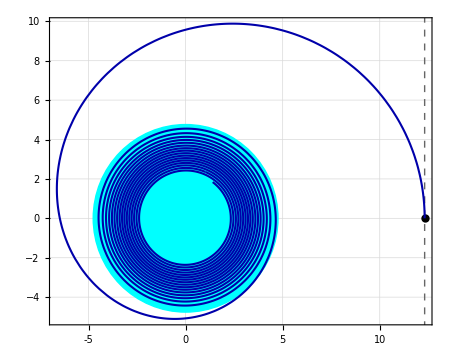

```mathematica
ThesisOrbitPlot[{rbarNumIn[t] Cos[phiNumIn[t]],rbarNumIn[t] Sin[phiNumIn[t]]},{t,t0,tFinish},rbarStar,"Fig_Orbit_With_r0","\\bar{r}(t)\\cos(\\phi(t))",(*Keeping default labels*)"\\bar{r}(t)\\sin(\\phi(t))",rbar0 (*This is your rbar0 value*)]
```

```mathematica
ThesisStandardPlotRadial[rbarNumIn[t],{t,0, tFinish},"Fig_radial","\\rb(t)","t", rbarStar]
```

ThesisStandardPlotRadial[InterpolatingFunction[{{0, 1704.88013526752528707278025503776016878020955196968835232179}}, <>][t],{t,0,1704.88013526752528707278025503776016878020955196968835232179},Fig_radial,\rb(t),t,47585207028263285547095886442410678645629/10000000000000000000000000000000000000000]

Saved Time Plot: /home/em/Documents/thesis/constant_density/Fig_Mach_Number_Evolution.pdf

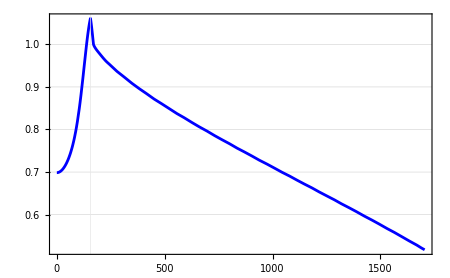

```mathematica
ThesisStandardPlotTime[Mach[rbarNumIn[t],urNumIn[t],uphiNumIn[t]],{t,0, tFinish},"Fig_Mach_Number_Evolution","\\mathcal{M}(t)","t", tSurface]
```

## Gravitational-wave strains

### h_+

#### formulae

```mathematica
hplusInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((Mfunc[r] Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Cos[2 phi])/r - rd^2 Cos[2phi] + 2rd r phid Sin[2phi] + (r phid)^2 Cos[2phi])
]
```

```mathematica
hplusFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hplusOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hplusInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

#### graph

Saved Standard (High-Precision): /home/em/Documents/thesis/constant_density/Fig_Gravitational_Wave_Plus.pdf

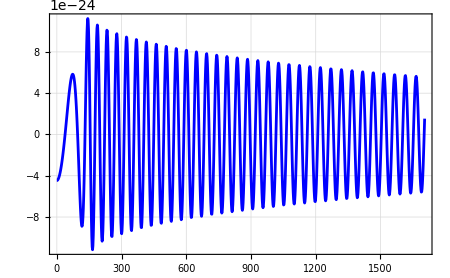

```mathematica
ThesisStandardPlot[hplusFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]],{t,0,tFinish},"Fig_Gravitational_Wave_Plus","h_{+}(t)","t",{},(*No labels for a single curve*)None,(*No special xTick*)1000,(*pPoints:High initial sampling for fast oscillations*)60       (*wPrec:High precision to resolve 10^-23 amplitudes*)]
```

### h_x

#### formulae

```mathematica
hxInside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarInside[rbar], rd, phid},
rd = drBardtInside[rbar,ur,uphi];
phid = dphidtInside[rbar,ur,uphi];
((-2m)/d)((Mfunc[r] Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxOutside[d_, m_, rbar_, ur_, uphi_, phi_] := Module[{r = rofrbarOutside[rbar], rd, phid},
rd = drBardt[rbar,ur,uphi];
phid = dphidtOutside[rbar,ur,uphi];
((-2m)/d)((M Sin[2 phi])/r - 2(rd Sin[phi] + r phid Cos[phi])(rd Cos[phi] - r phid Sin[phi]))
]
```

```mathematica
hxFull[d_, m_, rbar_, ur_, uphi_,phi_] := Piecewise[
{
{hxOutside[d, m, rbar, ur, uphi, phi], rbar >= rbarStar},
{hxInside[d, m, rbar, ur, uphi, phi], rbar < rbarStar}
}
]
```

#### graph

Saved Standard (High-Precision): /home/em/Documents/thesis/constant_density/Fig_Gravitational_Wave_Cross.pdf

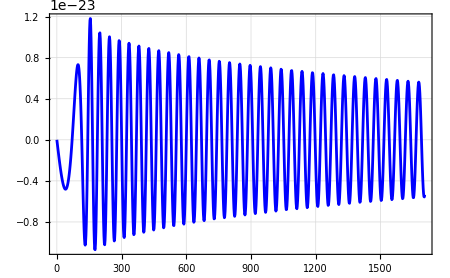

```mathematica
ThesisStandardPlot[hxFull[3 10^20,massNumIn[t],rbarNumIn[t],urNumIn[t],uphiNumIn[t],phiNumIn[t]],{t,0,tFinish},"Fig_Gravitational_Wave_Cross","h_{\\times}(t)","t",{},(*No labels for a single curve*)None,(*No special xTick*)1000,(*pPoints:High initial sampling for fast oscillations*)60       (*wPrec:High precision to resolve 10^-23 amplitudes*)]
```

```mathematica
(*Bundle your solutions and constants into a list*)dataToSave={rbarNumIn,urNumIn,phiNumIn,uphiNumIn,massNumIn,tFinish,tSurface};

(*Export using DumpSave-Note:DumpSave requires a Symbol or a list of Symbols*)
DumpSave[FileNameJoin[{exportDirectory,"constStarSim_Final.mx"}],{rbarNumIn,urNumIn,phiNumIn,uphiNumIn,massNumIn,tFinish,tSurface}];

Print[Style["Binary .mx file saved. Load speed: Instant.",Green,Bold]];
```

Binary .mx file saved. Load speed: Instant.

```mathematica
Get[FileNameJoin[exportDirectory, "constStarSim_Final.mx"]]
```